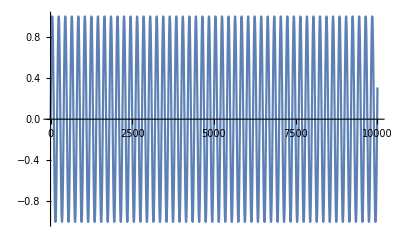

Fourier::fftl: Argument Sin[349.415 SawtoothWave[1.8 t]] is not a non-empty list or rectangular array of numeric quantities.

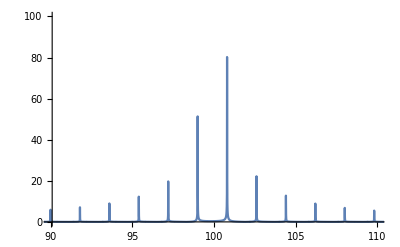

```mathematica
refresh = 1.8;
fc = 100.1;
trace = Sin[2π fc SawtoothWave[refresh t]/refresh];
xm = 100;
n = 50000;
x=Subdivide[0,xm,n];
f = (Range[n+1]-1)/xm;
ListPlot[trace/.t-> Subdivide[0,.5,10000],Joined->True]
ListPlot[Transpose[{f,Abs[Fourier[trace]/.t-> x]}],PlotRange->{{90,110},{0,100}},Joined->True]
```